```mathematica
n1=4;(*Number of populations*)
n2=4;(*Number of steps*)
phenotypelist=Tuples[{0,1},n1];
phenotypelist=DeleteCases[DeleteCases[phenotypelist,{1,1,1,1}],{0,0,0,0}];
comb1=Subsets[phenotypelist,{n2}];
comb=Select[comb1,Product[Total[Transpose[#][[i]]],{i,1,n1}]!=0&];
Length@comb
```

```mathematica
alpha1=Table[1,n2];
e={100,100,100,100}
alpha=alpha1*e
ct={0.001,0.001,0.001,0.001};
r=Table[1,n2+1];
Ig=Table[0.01,n1];
y=Table[0.1,n1];
S0=200000;
mout0=Join[{S0},Table[0,n2]];
X0={1,1,1,1};
p=1000;
Ct=Table[1/(1+(Sum[phenotypelist1[[i,j]]*ct[[j]]*alpha[[j]],{j,1,4}])^1),{i,1,Length@phenotypelist1}]
```

```mathematica
ClearAll[i]
V[[1]]
```

```mathematica
min
```

{{min11,min12,min13,min14,min15},{min21,min22,min23,min24,min25},{min31,min32,min33,min34,min35},{min41,min42,min43,min44,min45}}

```mathematica
t1=AbsoluteTime[];
Biolist={};
growthlist={};
Srate={};
fun1=p/(1+Exp[-h*(x-Total@X0)]);
fun2=((Total@X0-p)/(1+Exp[(x-h)/dx]))+p;
Do[phenotypelist1=comb[[k]];
Ct=Table[1/(1+(Sum[phenotypelist1[[i,j]]*ct[[j]]*e[[j]],{j,1,4}])^1),{i,1,Length@phenotypelist1}];
mout=Table[ToExpression["mout"<>ToString@j],{j,1,n2+1}];
V=Table[ToExpression["V"<>ToString@i],{i,1,n1}];
min=Table[ToExpression["min"<>ToString@i<>ToString@j],{i,1,n1},{j,1,n2+1}];
vs=Flatten@Table[phenotypelist1[[i,j]]*alpha[[j]],{i,1,n1},{j,1,1}];
vi=Table[phenotypelist1[[i,j]]*alpha[[j]]*min[[i,j]][t],{i,1,n1},{j,2,n2}];
vp=Table[Ig[[i]]*min[[i,n2+1]][t],{i,1,n2}];
v0=Table[0,{i,1,n2}];
v=Transpose@Join[{v0},{vs},Transpose@vi,{vp}];
g=Table[y[[i]]*(vp[[i]]*Ct[[i]]),{i,1,n1}];
var=Flatten@Join[mout,min,V];

mineqn={};
Veqn={};
Do[
mouteqn={};
Do[eqn1={min[[i,j]]'[t]==v[[i,j]]-v[[i,j+1]]+r[[j]]*(mout[[j]][t]-min[[i,j]][t])};
eqn2={mout[[j]]'[t]==-Sum[V[[i]][t]*r[[j]]*(mout[[j]][t]-min[[i,j]][t]),{i,1,n2}]};
mineqn=Join[mineqn,eqn1];
mouteqn=Join[mouteqn,eqn2];
,{j,1,n2+1}];
eqn3={V[[i]]'[t]==g[[i]]*V[[i]][t]*(1-Sum[V[[i]][t],{i,1,n1}]/p)};
Veqn=Join[Veqn,eqn3];
,{i,1,n1}];
NDeqn=Flatten@Join[mineqn,mouteqn,Veqn];
mineqn0={};
Veqn0={};
Do[
mouteqn0={};
Do[eqn01={min[[i,j]][0]==0};
eqn02={mout[[j]][0]==mout0[[j]]};
mineqn0=Join[mineqn0,eqn01];
mouteqn0=Join[mouteqn0,eqn02];
,{j,1,n2+1}];
eqn30={V[[i]][0]==X0[[i]]};
Veqn0=Join[Veqn0,eqn30];
,{i,1,n1}];
NDeqn0=Flatten@Join[mineqn0,mouteqn0,Veqn0];

eqn=Join[NDeqn,NDeqn0];
result=NDSolve[eqn,var,{t,0,6000}];
Grocurve=Plot[Evaluate[Table[V[[i]][t],{i,1,n1}]/.result],{t,0,3000},PlotRange->{-5,1000},PlotLegends->Table[ToString@phenotypelist1[[i]],{i,1,n1}],PlotStyle->Thickness[0.01],Frame->True,AspectRatio->1,FrameStyle->Directive[Thickness[0.005],Black,Bold,36],LabelStyle->Directive[Black,Bold,36],ImageSize->Large,AxesLabel->{"Time","Relative Abundance"}];
Bio=Join[First@Evaluate[Table[V[[i]][6000],{i,1,n1}]/.result],Evaluate[Total@Table[V[[i]][6000],{i,1,n1}]/.result]];
Sconsume=First[Evaluate[mout[[1]]'[6000]/.result]];
Sconsume1=First[S0-Evaluate[mout[[1]][6000]/.result]]/6000;

(*grocurve=Select[Table[Evaluate[First@Total[Table[V[[i]][t]/.result,{i,1,n}]]],{t,0,3000,0.1}],#<999.99999&];
fit=NonlinearModelFit[grocurve,fun1,h,x];
growthrate={fit["AdjustedRSquared"],h/.fit["BestFitParameters"]};*)

grocurve=Select[Table[Evaluate[First@Total[Table[V[[i]][t]/.result,{i,1,n1}]]],{t,0,3000,0.1}],#<999.99999&];
fit=NonlinearModelFit[grocurve,fun2,{h,dx},x];
para=h/.fit["BestFitParameters"];
lagtime=x1/.First@First@Solve[Total@X0-fit[para]==fit'[para](x1-para),x1];
growthrate={fit["AdjustedRSquared"],para,fit'[para],lagtime};

growthlist=Join[growthlist,{growthrate}];
Biolist=Join[Biolist,{Bio}];
Srate=Join[Srate,{{Sconsume,Sconsume1}}];
,{k,1,1}];
t2=AbsoluteTime[];
costT=t2-t1
```

General::munfl: 1/(8.21841×10^307) is too small to represent as a normalized machine number; precision may be lost.

0.5275904

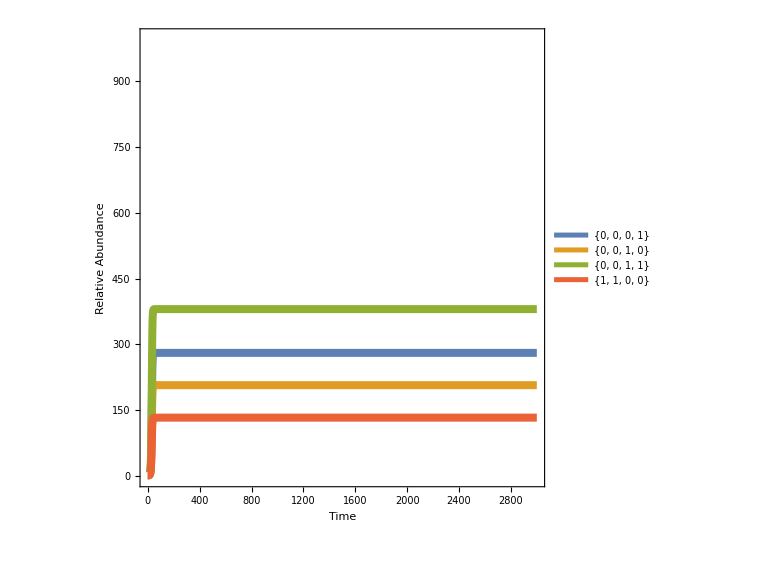

```mathematica
Grocurve
```

```mathematica
var
```